```mathematica
dir="D:\\workingBuffer 2";
```

```mathematica
dir="D:\\newLight3";
```

```mathematica
indexOfEgg=6;
```

```mathematica
GetNumberOfOrganisms[frameNo_]:=Module[{path,file,headings,applyHeading,items,nOrganisms,nFertile},
path = StringForm["``\\output\\frame``.csv",dir,frameNo];
file=Import[path//ToString];
headings=file//First;
items=file//Rest;
applyHeading[item_]:=MapThread[#1-> #2&,{headings,item}];
items = applyHeading/@items;
nOrganisms=Select["o"/.items,#≥0&]//CountDistinct;
nFertile=Cases[{"o","ct"}/.items,{o_/;o≥0,indexOfEgg}->o]//CountDistinct;
{nOrganisms,nFertile}
]
```

```mathematica
GetCellsPerOrganism[frameNo_]:=Module[{path,file,headings,applyHeading,items,nOrganisms,nCells},
path = StringForm["``\\output\\frame``.csv",dir,frameNo];
file=Import[path//ToString];
headings=file//First;
items=file//Rest;
applyHeading[item_]:=MapThread[#1-> #2&,{headings,item}];
items = applyHeading/@items;
nOrganisms=Select["o"/.items,#≥0&]//CountDistinct;
nCells =items//Length;
nCells/nOrganisms
]
```

```mathematica
GetEggsPerOrganism[frameNo_]:=Module[{path,file,headings,applyHeading,items,nOrganisms,nEggs},
path = StringForm["``\\output\\frame``.csv",dir,frameNo];
file=Import[path//ToString];
headings=file//First;
items=file//Rest;
applyHeading[item_]:=MapThread[#1-> #2&,{headings,item}];
items = applyHeading/@items;
nOrganisms=Select["o"/.items,#≥0&]//CountDistinct;
nEggs=Count[{"o","ct"}/.items, {o_/;o≥0,indexOfEgg}];
nEggs/nOrganisms
]
```

```mathematica
GetNumberOfOrganisms[200000]
```

{2373,2044}

```mathematica
f0=0;
fMax=1160000;
df=10000;
GetNumberOfOrganisms[fMax]//Print;
frames=Table[f,{f,f0,fMax,df}];
nOrgsList=ParallelMap[GetNumberOfOrganisms,frames]//Transpose;
```

{3880,3643}

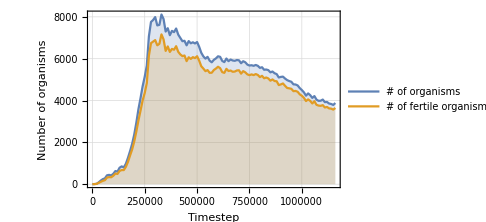

```mathematica
plot=ListPlot[
nOrgsList,
DataRange->{f0,fMax},
Filling->Bottom,
Joined->True,
PlotRange->Full,
Frame->{{True,False},{True,False}},
FrameLabel->{"Timestep","Number of organisms"},
PlotLegends->Placed[{"# of organisms","# of fertile organisms"},Above],
ImageSize->Medium,
GridLines->Automatic
]
```

```mathematica
Export["C:\\Users\\admin\\Documents\\Joakim\\repo\\grafiliv\\doc\\figs\\nOrgs over time\\nOrgs.eps",plot];
```

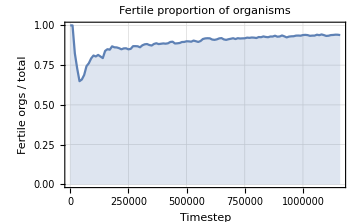

```mathematica
plot1=ListPlot[
Last[#]/First[#]&/@Transpose[nOrgsList],
DataRange->{f0,fMax},
Filling->Bottom,
Joined->True,
PlotRange->{0,1},
Frame->{{True,False},{True,False}},
PlotLabel->"Fertile proportion of organisms",
FrameLabel->{"Timestep","Fertile orgs / total"},
ImageSize->Medium,
GridLines->Automatic
]
```

```mathematica
Export["C:\\Users\\admin\\Documents\\Joakim\\repo\\grafiliv\\doc\\figs\\nOrgs over time\\fertileProp.eps",plot1];
```

```mathematica
cellFreqList=ParallelMap[GetCellsPerOrganism,frames];
```

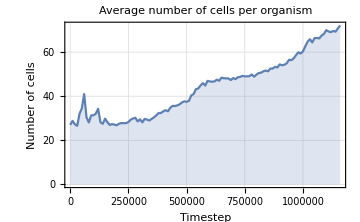

```mathematica
plot2=ListPlot[
cellFreqList,
DataRange->{f0,fMax},
Filling->Bottom,
Joined->True,
PlotRange->Full,
Frame->{{True,False},{True,False}},
PlotLabel->"Average number of cells per organism",
FrameLabel->{"Timestep","Number of cells"},
ImageSize->Medium,
GridLines->Automatic
]
```

```mathematica
Export["C:\\Users\\admin\\Documents\\Joakim\\repo\\grafiliv\\doc\\figs\\nOrgs over time\\nCells.eps",plot2];
```

```mathematica
eggFreqList=ParallelMap[GetEggsPerOrganism,frames];
```

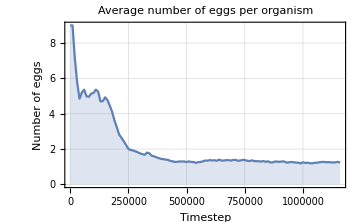

```mathematica
plot3=ListPlot[
eggFreqList,
DataRange->{f0,fMax},
Filling->Bottom,
Joined->True,
PlotRange->Full,
Frame->{{True,False},{True,False}},
PlotLabel->"Average number of eggs per organism",
FrameLabel->{"Timestep","Number of eggs"},
ImageSize->Medium,
GridLines->Automatic
]
```

```mathematica
Export["C:\\Users\\admin\\Documents\\Joakim\\repo\\grafiliv\\doc\\figs\\nOrgs over time\\nEggs.eps",plot3];
```